## Set up

### Local Work Environment

Code last run on:

```mathematica
DateString[]
```

Thu 18 Aug 2016 18:26:00

```mathematica
$Version
```

11.0.0 for Microsoft Windows (64-bit) (July 28, 2016)

### Load Package

```mathematica
With[
{
packageFileName=
FileNameJoin[
{
ParentDirectory@NotebookDirectory[],
"HDF5.Mathematica.Packages",
"HDF5HighLevel.m"
}
]
},

Needs["HDF5HighLevel`",packageFileName]

]
```

```mathematica
$HDF5packageVersion
```

V2.0

```mathematica
H5BasicGetLibVersion[]
```

{1,8,17}

## General Information

```mathematica
filename=FileNameJoin[{NotebookDirectory[],"MOD02HKM.A2013060.1455.006.2014224104953.h5"}]
```

C:\Users\smartin\Desktop\HDF5WrappersForMathematica  Ver 19 August 2016\4 HDF5 Real Case Studies\MOD02HKM.A2013060.1455.006.2014224104953.h5

```mathematica
CompoundExpression[

Print["NamesAndTypes"],
Print[namesAndTypes=NamesAndTypes[filename]],

Print["\nDataSetsMetaData"],
Print[dataSetsMetaData=DataSetsMetaData[filename]],

numberOfDatasets=Replace["NumberOfDatasets",dataSetsMetaData],
namesOfDatasets=Replace["DatasetName",dataSetsMetaData],
classesOfDatasets=Replace["DatasetClassType",dataSetsMetaData],

Print["\nAttributes"],
Do[
With[{attributeName=namesOfDatasets⟦i⟧},
CompoundExpression[
Print["Attribute: ",attributeName],
Print[ReadAttributes[filename,attributeName,"ReturnValues"->True]]
]
],
{i,numberOfDatasets}
]
]
```

NamesAndTypes

{DATASET→{./Band_250M,./Band_500M,./Change in relative responses of thermal detectors,./DC Restore Change for Reflective 1km Bands,./DC Restore Change for Reflective 250m Bands,./DC Restore Change for Reflective 500m Bands,./DC Restore Change for Thermal Bands,./Level 1B Swath Metadata,./Noise in Thermal Detectors,./MODIS_SWATH_Type_L1B/Data Fields/Band_250M,./MODIS_SWATH_Type_L1B/Data Fields/Band_500M,./MODIS_SWATH_Type_L1B/Data Fields/EV_250_Aggr500_RefSB,./MODIS_SWATH_Type_L1B/Data Fields/EV_250_Aggr500_RefSB_Samples_Used,./MODIS_SWATH_Type_L1B/Data Fields/EV_250_Aggr500_RefSB_Uncert_Indexes,./MODIS_SWATH_Type_L1B/Data Fields/EV_500_RefSB,./MODIS_SWATH_Type_L1B/Data Fields/EV_500_RefSB_Uncert_Indexes,./MODIS_SWATH_Type_L1B/Geolocation Fields/Latitude,./MODIS_SWATH_Type_L1B/Geolocation Fields/Longitude},GROUP→{./HDF4_DIMGROUP,./MODIS_SWATH_Type_L1B,./MODIS_SWATH_Type_L1B/Data Fields,./MODIS_SWATH_Type_L1B/Geolocation Fields,./MODIS_SWATH_Type_L1B/Swath Attributes},NAMED_DATATYPE→{./Level 1B Swath Metadata_t,./MODIS_SWATH_Type_L1B/Data Fields/Band_250M_t,./MODIS_SWATH_Type_L1B/Data Fields/Band_500M_t}}

DataSetsMetaData

{NumberOfDatasets→18,DatasetName→{./Band_250M,./Band_500M,./Change in relative responses of thermal detectors,./DC Restore Change for Reflective 1km Bands,./DC Restore Change for Reflective 250m Bands,./DC Restore Change for Reflective 500m Bands,./DC Restore Change for Thermal Bands,./Level 1B Swath Metadata,./Noise in Thermal Detectors,./MODIS_SWATH_Type_L1B/Data Fields/Band_250M,./MODIS_SWATH_Type_L1B/Data Fields/Band_500M,./MODIS_SWATH_Type_L1B/Data Fields/EV_250_Aggr500_RefSB,./MODIS_SWATH_Type_L1B/Data Fields/EV_250_Aggr500_RefSB_Samples_Used,./MODIS_SWATH_Type_L1B/Data Fields/EV_250_Aggr500_RefSB_Uncert_Indexes,./MODIS_SWATH_Type_L1B/Data Fields/EV_500_RefSB,./MODIS_SWATH_Type_L1B/Data Fields/EV_500_RefSB_Uncert_Indexes,./MODIS_SWATH_Type_L1B/Geolocation Fields/Latitude,./MODIS_SWATH_Type_L1B/Geolocation Fields/Longitude},DatasetClassType→{FLOAT,FLOAT,INTEGER,INTEGER,INTEGER,INTEGER,INTEGER,COMPOUND,INTEGER,COMPOUND,COMPOUND,INTEGER,INTEGER,INTEGER,INTEGER,INTEGER,FLOAT,FLOAT},DatasetSystemType→{System.Single[],System.Single[],System.Byte[],System.SByte[],System.SByte[],System.SByte[],System.SByte[],System.Byte[],System.Byte[],System.Byte[],System.Byte[],System.UInt16[],System.SByte[],System.Byte[],System.UInt16[],System.Byte[],System.Single[],System.Single[]},DatasetSpaceDimensions→{{2},{5},{16,10},{203,15,10},{203,2,40},{203,5,20},{203,16,10},{203},{16,10},{2},{5},{2,4060,2708},{2,4060,2708},{2,4060,2708},{5,4060,2708},{5,4060,2708},{2030,1354},{2030,1354}}}

Attributes

Attribute: ./Band_250M

{NumberOfAttributes→4,AttributeName→{HDF4_OBJECT_NAME,HDF4_OBJECT_TYPE,HDF4_REF_NUM,long_name},AttributeClassType→{STRING,STRING,INTEGER,STRING},AttributeSystemType→{System.Byte[],System.Byte[],System.UInt16[],System.Byte[]},AttributeSystemTypeCountInOneDatum→{9,3,1,32},AttributeSpaceDimensions→{{},{},{},{}},AttributeValues→{Band_250M,SDS,6096,250M Band Numbers for Subsetting}}

Attribute: ./Band_500M

{NumberOfAttributes→4,AttributeName→{HDF4_OBJECT_NAME,HDF4_OBJECT_TYPE,HDF4_REF_NUM,long_name},AttributeClassType→{STRING,STRING,INTEGER,STRING},AttributeSystemType→{System.Byte[],System.Byte[],System.UInt16[],System.Byte[]},AttributeSystemTypeCountInOneDatum→{9,3,1,32},AttributeSpaceDimensions→{{},{},{},{}},AttributeValues→{Band_500M,SDS,6098,500M Band Numbers for Subsetting}}

Attribute: ./Change in relative responses of thermal detectors

{NumberOfAttributes→4,AttributeName→{DIMENSION_NAMELIST,HDF4_OBJECT_NAME,HDF4_OBJECT_TYPE,HDF4_REF_NUM},AttributeClassType→{STRING,STRING,STRING,INTEGER},AttributeSystemType→{System.Byte[],System.Byte[],System.Byte[],System.UInt16[]},AttributeSystemTypeCountInOneDatum→{276,49,3,1},AttributeSpaceDimensions→{{2},{},{},{}},AttributeValues→{{/HDF4_DIMGROUP/number of emissive bands,/HDF4_DIMGROUP/detectors per 1km band},Change in relative responses of thermal detectors,SDS,6102}}

Attribute: ./DC Restore Change for Reflective 1km Bands

{NumberOfAttributes→4,AttributeName→{DIMENSION_NAMELIST,HDF4_OBJECT_NAME,HDF4_OBJECT_TYPE,HDF4_REF_NUM},AttributeClassType→{STRING,STRING,STRING,INTEGER},AttributeSystemType→{System.Byte[],System.Byte[],System.Byte[],System.UInt16[]},AttributeSystemTypeCountInOneDatum→{276,42,3,1},AttributeSpaceDimensions→{{3},{},{},{}},AttributeValues→{{/HDF4_DIMGROUP/number of scans,/HDF4_DIMGROUP/number of 1km reflective bands,/HDF4_DIMGROUP/detectors per 1km band},DC Restore Change for Reflective 1km Bands,SDS,6110}}

Attribute: ./DC Restore Change for Reflective 250m Bands

{NumberOfAttributes→4,AttributeName→{DIMENSION_NAMELIST,HDF4_OBJECT_NAME,HDF4_OBJECT_TYPE,HDF4_REF_NUM},AttributeClassType→{STRING,STRING,STRING,INTEGER},AttributeSystemType→{System.Byte[],System.Byte[],System.Byte[],System.UInt16[]},AttributeSystemTypeCountInOneDatum→{276,43,3,1},AttributeSpaceDimensions→{{3},{},{},{}},AttributeValues→{{/HDF4_DIMGROUP/number of scans,/HDF4_DIMGROUP/number of 250m bands,/HDF4_DIMGROUP/detectors per 250m band},DC Restore Change for Reflective 250m Bands,SDS,6106}}

Attribute: ./DC Restore Change for Reflective 500m Bands

{NumberOfAttributes→4,AttributeName→{DIMENSION_NAMELIST,HDF4_OBJECT_NAME,HDF4_OBJECT_TYPE,HDF4_REF_NUM},AttributeClassType→{STRING,STRING,STRING,INTEGER},AttributeSystemType→{System.Byte[],System.Byte[],System.Byte[],System.UInt16[]},AttributeSystemTypeCountInOneDatum→{276,43,3,1},AttributeSpaceDimensions→{{3},{},{},{}},AttributeValues→{{/HDF4_DIMGROUP/number of scans,/HDF4_DIMGROUP/number of 500m bands,/HDF4_DIMGROUP/detectors per 500m band},DC Restore Change for Reflective 500m Bands,SDS,6108}}

Attribute: ./DC Restore Change for Thermal Bands

{NumberOfAttributes→4,AttributeName→{DIMENSION_NAMELIST,HDF4_OBJECT_NAME,HDF4_OBJECT_TYPE,HDF4_REF_NUM},AttributeClassType→{STRING,STRING,STRING,INTEGER},AttributeSystemType→{System.Byte[],System.Byte[],System.Byte[],System.UInt16[]},AttributeSystemTypeCountInOneDatum→{276,35,3,1},AttributeSpaceDimensions→{{3},{},{},{}},AttributeValues→{{/HDF4_DIMGROUP/number of scans,/HDF4_DIMGROUP/number of emissive bands,/HDF4_DIMGROUP/detectors per 1km band},DC Restore Change for Thermal Bands,SDS,6104}}

Attribute: ./Level 1B Swath Metadata

{NumberOfAttributes→20,AttributeName→{CLASS,FIELD_0_NAME,FIELD_10_NAME,FIELD_11_NAME,FIELD_12_NAME,FIELD_13_NAME,FIELD_1_NAME,FIELD_2_NAME,FIELD_3_NAME,FIELD_4_NAME,FIELD_5_NAME,FIELD_6_NAME,FIELD_7_NAME,FIELD_8_NAME,FIELD_9_NAME,HDF4_OBJECT_NAME,HDF4_OBJECT_TYPE,HDF4_REF_NUM,TITLE,VERSION},AttributeClassType→{STRING,STRING,STRING,STRING,STRING,STRING,STRING,STRING,STRING,STRING,STRING,STRING,STRING,STRING,STRING,STRING,STRING,INTEGER,STRING,STRING},AttributeSystemType→{System.Byte[],System.Byte[],System.Byte[],System.Byte[],System.Byte[],System.Byte[],System.Byte[],System.Byte[],System.Byte[],System.Byte[],System.Byte[],System.Byte[],System.Byte[],System.Byte[],System.Byte[],System.Byte[],System.Byte[],System.UInt16[],System.Byte[],System.Byte[]},AttributeSystemTypeCountInOneDatum→{5,11,27,30,12,21,18,9,11,20,9,18,23,24,28,23,5,1,23,3},AttributeSpaceDimensions→{{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{}},AttributeValues→{TABLE,Scan Number,Solar Zenith of Nadir Frame,No. OBC BB thermistor outliers,Bit QA Flags,Sector Rotation Angle,Complete Scan Flag,Scan Type,Mirror Side,EV Sector Start Time,EV_Frames,Nadir_Frame_Number,Latitude of Nadir Frame,Longitude of Nadir Frame,Solar Azimuth of Nadir Frame,Level 1B Swath Metadata,Vdata,6112,Level 1B Swath Metadata,1.0}}

Attribute: ./Noise in Thermal Detectors

{NumberOfAttributes→4,AttributeName→{DIMENSION_NAMELIST,HDF4_OBJECT_NAME,HDF4_OBJECT_TYPE,HDF4_REF_NUM},AttributeClassType→{STRING,STRING,STRING,INTEGER},AttributeSystemType→{System.Byte[],System.Byte[],System.Byte[],System.UInt16[]},AttributeSystemTypeCountInOneDatum→{276,26,3,1},AttributeSpaceDimensions→{{2},{},{},{}},AttributeValues→{{/HDF4_DIMGROUP/number of emissive bands,/HDF4_DIMGROUP/detectors per 1km band},Noise in Thermal Detectors,SDS,6100}}

Attribute: ./MODIS_SWATH_Type_L1B/Data Fields/Band_250M

{NumberOfAttributes→7,AttributeName→{CLASS,FIELD_0_NAME,HDF4_OBJECT_NAME,HDF4_OBJECT_TYPE,HDF4_REF_NUM,TITLE,VERSION},AttributeClassType→{STRING,STRING,STRING,STRING,INTEGER,STRING,STRING},AttributeSystemType→{System.Byte[],System.Byte[],System.Byte[],System.Byte[],System.UInt16[],System.Byte[],System.Byte[]},AttributeSystemTypeCountInOneDatum→{5,9,9,5,1,9,3},AttributeSpaceDimensions→{{},{},{},{},{},{},{}},AttributeValues→{TABLE,Band_250M,Band_250M,Vdata,6093,Band_250M,1.0}}

Attribute: ./MODIS_SWATH_Type_L1B/Data Fields/Band_500M

{NumberOfAttributes→7,AttributeName→{CLASS,FIELD_0_NAME,HDF4_OBJECT_NAME,HDF4_OBJECT_TYPE,HDF4_REF_NUM,TITLE,VERSION},AttributeClassType→{STRING,STRING,STRING,STRING,INTEGER,STRING,STRING},AttributeSystemType→{System.Byte[],System.Byte[],System.Byte[],System.Byte[],System.UInt16[],System.Byte[],System.Byte[]},AttributeSystemTypeCountInOneDatum→{5,9,9,5,1,9,3},AttributeSpaceDimensions→{{},{},{},{},{},{},{}},AttributeValues→{TABLE,Band_500M,Band_500M,Vdata,6094,Band_500M,1.0}}

Attribute: ./MODIS_SWATH_Type_L1B/Data Fields/EV_250_Aggr500_RefSB

{NumberOfAttributes→18,AttributeName→{DIMENSION_NAMELIST,HDF4_OBJECT_NAME,HDF4_OBJECT_TYPE,HDF4_REF_NUM,_FillValue,band_names,corrected_counts_offsets,corrected_counts_scales,corrected_counts_units,long_name,radiance_offsets,radiance_scales,radiance_units,reflectance_offsets,reflectance_scales,reflectance_units,units,valid_range},AttributeClassType→{STRING,STRING,STRING,INTEGER,INTEGER,STRING,FLOAT,FLOAT,STRING,STRING,FLOAT,FLOAT,STRING,FLOAT,FLOAT,STRING,STRING,INTEGER},AttributeSystemType→{System.Byte[],System.Byte[],System.Byte[],System.UInt16[],System.UInt16[],System.Byte[],System.Single[],System.Single[],System.Byte[],System.Byte[],System.Single[],System.Single[],System.Byte[],System.Single[],System.Single[],System.Byte[],System.Byte[],System.UInt16[]},AttributeSystemTypeCountInOneDatum→{276,20,3,1,1,3,1,1,6,70,1,1,30,1,1,4,4,1},AttributeSpaceDimensions→{{3},{},{},{},{},{},{2},{2},{},{},{2},{2},{},{2},{2},{},{},{2}},AttributeValues→{{/HDF4_DIMGROUP/Band_250M:MODIS_SWATH_Type_L1B,/HDF4_DIMGROUP/20*nscans:MODIS_SWATH_Type_L1B,/HDF4_DIMGROUP/2*Max_EV_frames:MODIS_SWATH_Type_L1B},EV_250_Aggr500_RefSB,SDS,4467,65535,1,2,{0.,0.},{0.124973,0.124973},counts,Earth View 250M Aggregated 500M Reflective Solar Bands Scaled Integers,{0.,0.},{0.0275048,0.0103067},Watts/m^2/micrometer/steradian,{0.,0.},{0.000052829,0.0000320462},none,none,{0,32767}}}

Attribute: ./MODIS_SWATH_Type_L1B/Data Fields/EV_250_Aggr500_RefSB_Samples_Used

{NumberOfAttributes→8,AttributeName→{DIMENSION_NAMELIST,HDF4_OBJECT_NAME,HDF4_OBJECT_TYPE,HDF4_REF_NUM,_FillValue,long_name,units,valid_range},AttributeClassType→{STRING,STRING,STRING,INTEGER,INTEGER,STRING,STRING,INTEGER},AttributeSystemType→{System.Byte[],System.Byte[],System.Byte[],System.UInt16[],System.SByte[],System.Byte[],System.Byte[],System.SByte[]},AttributeSystemTypeCountInOneDatum→{276,33,3,1,1,92,4,1},AttributeSpaceDimensions→{{3},{},{},{},{},{},{},{2}},AttributeValues→{{/HDF4_DIMGROUP/Band_250M:MODIS_SWATH_Type_L1B,/HDF4_DIMGROUP/20*nscans:MODIS_SWATH_Type_L1B,/HDF4_DIMGROUP/2*Max_EV_frames:MODIS_SWATH_Type_L1B},EV_250_Aggr500_RefSB_Samples_Used,SDS,6091,-1,Earth View 250M Aggregated 500M Reflective Solar Bands Number of Samples Used in Aggregation,none,{0,6}}}

Attribute: ./MODIS_SWATH_Type_L1B/Data Fields/EV_250_Aggr500_RefSB_Uncert_Indexes

{NumberOfAttributes→11,AttributeName→{DIMENSION_NAMELIST,HDF4_OBJECT_NAME,HDF4_OBJECT_TYPE,HDF4_REF_NUM,_FillValue,long_name,scaling_factor,specified_uncertainty,uncertainty_units,units,valid_range},AttributeClassType→{STRING,STRING,STRING,INTEGER,INTEGER,STRING,FLOAT,FLOAT,STRING,STRING,INTEGER},AttributeSystemType→{System.Byte[],System.Byte[],System.Byte[],System.UInt16[],System.Byte[],System.Byte[],System.Single[],System.Single[],System.Byte[],System.Byte[],System.Byte[]},AttributeSystemTypeCountInOneDatum→{276,35,3,1,1,74,1,1,7,4,1},AttributeSpaceDimensions→{{3},{},{},{},{},{},{2},{2},{},{},{2}},AttributeValues→{{/HDF4_DIMGROUP/Band_250M:MODIS_SWATH_Type_L1B,/HDF4_DIMGROUP/20*nscans:MODIS_SWATH_Type_L1B,/HDF4_DIMGROUP/2*Max_EV_frames:MODIS_SWATH_Type_L1B},EV_250_Aggr500_RefSB_Uncert_Indexes,SDS,5279,255,Earth View 250M Aggregated 500M Reflective Solar Bands Uncertainty Indexes,{7.,7.},{1.5,1.5},percent,none,{0,15}}}

Attribute: ./MODIS_SWATH_Type_L1B/Data Fields/EV_500_RefSB

{NumberOfAttributes→18,AttributeName→{DIMENSION_NAMELIST,HDF4_OBJECT_NAME,HDF4_OBJECT_TYPE,HDF4_REF_NUM,_FillValue,band_names,corrected_counts_offsets,corrected_counts_scales,corrected_counts_units,long_name,radiance_offsets,radiance_scales,radiance_units,reflectance_offsets,reflectance_scales,reflectance_units,units,valid_range},AttributeClassType→{STRING,STRING,STRING,INTEGER,INTEGER,STRING,FLOAT,FLOAT,STRING,STRING,FLOAT,FLOAT,STRING,FLOAT,FLOAT,STRING,STRING,INTEGER},AttributeSystemType→{System.Byte[],System.Byte[],System.Byte[],System.UInt16[],System.UInt16[],System.Byte[],System.Single[],System.Single[],System.Byte[],System.Byte[],System.Single[],System.Single[],System.Byte[],System.Single[],System.Single[],System.Byte[],System.Byte[],System.UInt16[]},AttributeSystemTypeCountInOneDatum→{276,12,3,1,1,9,1,1,6,54,1,1,30,1,1,4,4,1},AttributeSpaceDimensions→{{3},{},{},{},{},{},{5},{5},{},{},{5},{5},{},{5},{5},{},{},{2}},AttributeValues→{{/HDF4_DIMGROUP/Band_500M:MODIS_SWATH_Type_L1B,/HDF4_DIMGROUP/20*nscans:MODIS_SWATH_Type_L1B,/HDF4_DIMGROUP/2*Max_EV_frames:MODIS_SWATH_Type_L1B},EV_500_RefSB,SDS,408,65535,3,4,5,6,7,{0.,0.,0.,0.,0.},{0.124973,0.124973,0.124973,0.124973,0.124973},counts,Earth View 500M Reflective Solar Bands Scaled Integers,{0.,0.,0.,0.,0.},{0.0365172,0.0252029,0.00589534,0.0026768,0.000824785},Watts/m^2/micrometer/steradian,{0.,0.,0.,0.,0.},{0.0000539554,0.0000416685,0.0000383416,0.0000343751,0.0000281701},none,none,{0,32767}}}

Attribute: ./MODIS_SWATH_Type_L1B/Data Fields/EV_500_RefSB_Uncert_Indexes

{NumberOfAttributes→11,AttributeName→{DIMENSION_NAMELIST,HDF4_OBJECT_NAME,HDF4_OBJECT_TYPE,HDF4_REF_NUM,_FillValue,long_name,scaling_factor,specified_uncertainty,uncertainty_units,units,valid_range},AttributeClassType→{STRING,STRING,STRING,INTEGER,INTEGER,STRING,FLOAT,FLOAT,STRING,STRING,INTEGER},AttributeSystemType→{System.Byte[],System.Byte[],System.Byte[],System.UInt16[],System.Byte[],System.Byte[],System.Single[],System.Single[],System.Byte[],System.Byte[],System.Byte[]},AttributeSystemTypeCountInOneDatum→{276,27,3,1,1,58,1,1,7,4,1},AttributeSpaceDimensions→{{3},{},{},{},{},{},{5},{5},{},{},{2}},AttributeValues→{{/HDF4_DIMGROUP/Band_500M:MODIS_SWATH_Type_L1B,/HDF4_DIMGROUP/20*nscans:MODIS_SWATH_Type_L1B,/HDF4_DIMGROUP/2*Max_EV_frames:MODIS_SWATH_Type_L1B},EV_500_RefSB_Uncert_Indexes,SDS,2437,255,Earth View 500M Reflective Solar Bands Uncertainty Indexes,{7.,7.,5.,5.,5.},{1.5,1.5,1.5,1.5,1.5},percent,none,{0,15}}}

Attribute: ./MODIS_SWATH_Type_L1B/Geolocation Fields/Latitude

{NumberOfAttributes→7,AttributeName→{DIMENSION_NAMELIST,HDF4_OBJECT_NAME,HDF4_OBJECT_TYPE,HDF4_REF_NUM,_FillValue,units,valid_range},AttributeClassType→{STRING,STRING,STRING,INTEGER,FLOAT,STRING,FLOAT},AttributeSystemType→{System.Byte[],System.Byte[],System.Byte[],System.UInt16[],System.Single[],System.Byte[],System.Single[]},AttributeSystemTypeCountInOneDatum→{276,8,3,1,1,7,1},AttributeSpaceDimensions→{{2},{},{},{},{},{},{2}},AttributeValues→{{/HDF4_DIMGROUP/10*nscans:MODIS_SWATH_Type_L1B,/HDF4_DIMGROUP/Max_EV_frames:MODIS_SWATH_Type_L1B},Latitude,SDS,4,-999.,degrees,{-90.,90.}}}

Attribute: ./MODIS_SWATH_Type_L1B/Geolocation Fields/Longitude

{NumberOfAttributes→7,AttributeName→{DIMENSION_NAMELIST,HDF4_OBJECT_NAME,HDF4_OBJECT_TYPE,HDF4_REF_NUM,_FillValue,units,valid_range},AttributeClassType→{STRING,STRING,STRING,INTEGER,FLOAT,STRING,FLOAT},AttributeSystemType→{System.Byte[],System.Byte[],System.Byte[],System.UInt16[],System.Single[],System.Byte[],System.Single[]},AttributeSystemTypeCountInOneDatum→{276,9,3,1,1,7,1},AttributeSpaceDimensions→{{2},{},{},{},{},{},{2}},AttributeValues→{{/HDF4_DIMGROUP/10*nscans:MODIS_SWATH_Type_L1B,/HDF4_DIMGROUP/Max_EV_frames:MODIS_SWATH_Type_L1B},Longitude,SDS,204,-999.,degrees,{-180.,180.}}}

```mathematica
ReadAttributes[filename,".","ReturnValues"->False]
```

{NumberOfAttributes→58,AttributeName→{% Dead Detector EV Data_GLOSDS,% Dead Subframe EV Data_GLOSDS,% EV Data Not Calibrated_GLOSDS,% EV Data Where Cannot Compute BG DN_GLOSDS,% EV Data Where Nadir Door Closed_GLOSDS,% L1A EV All Scan Data are Missing_GLOSDS,% L1A EV DN Missing Within Scan_GLOSDS,% L1A EV RSB DN Not in Day Mode_GLOSDS,% RSB EV Data With dn** Below Scale_GLOSDS,% Saturated EV Data_GLOSDS,% Sector Rotation EV Data_GLOSDS,% TEB EV Data With Moon in SVP_GLOSDS,%Saturated EV Observations_GLOSDS,%Valid EV Observations_GLOSDS,ArchiveMetadata.0_GLOSDS,Bit QA Flags Change_GLOSDS,Bit QA Flags Last Value_GLOSDS,CoreMetadata.0_GLOSDS,Dead Detector List_GLOSDS,Dead Subframe List_GLOSDS,Detector Quality Flag2_GLOSDS,Detector Quality Flag_GLOSDS,Doors and Screens Configuration_GLOSDS,Earth-Sun Distance_GLOSDS,Electronics Configuration Change_GLOSDS,Electronics Redundancy Vector_GLOSDS,Emissive Bands With Bad Data_GLOSDS,Emissive LUT Serial Number and Date of Last Change_GLOSDS,Focal Plane Set Point State_GLOSDS,Granule Average QA Values_GLOSDS,HDFEOSVersion_GLOSDS,HDFEOS_FractionalOffset_2*Max_EV_frames_MODIS_SWATH_Type_L1B_GLOSDS,HDFEOS_FractionalOffset_20*nscans_MODIS_SWATH_Type_L1B_GLOSDS,Incomplete Scans_GLOSDS,Max Earth View Frames_GLOSDS,Noise in Average BB Temperature_GLOSDS,Noise in Black Body Thermistors_GLOSDS,Noise in Cavity Temperature_GLOSDS,Noise in Instrument Temperature_GLOSDS,Noise in LWIR FPA Temperature_GLOSDS,Noise in MWIR FPA Temperature_GLOSDS,Noise in Scan Mirror Thermistor #1_GLOSDS,Noise in Scan Mirror Thermistor #2_GLOSDS,Noise in Scan Mirror Thermistor Average_GLOSDS,Noise in Temperature of NIR FPA_GLOSDS,Noise in Temperature of Vis FPA_GLOSDS,Noisy Detector List_GLOSDS,Noisy Subframe List_GLOSDS,Number of Day mode scans_GLOSDS,Number of Night mode scans_GLOSDS,Number of Scans_GLOSDS,QA LUT Serial Number and Date of Last Change_GLOSDS,Reflective Bands With Bad Data_GLOSDS,Reflective LUT Serial Number and Date of Last Change_GLOSDS,Solar Irradiance on RSB Detectors over pi_GLOSDS,StructMetadata.0_GLOSDS,identifier_product_doi_GLOSDS,identifier_product_doi_authority_GLOSDS},AttributeClassType→{FLOAT,FLOAT,FLOAT,FLOAT,FLOAT,FLOAT,FLOAT,FLOAT,FLOAT,FLOAT,FLOAT,FLOAT,FLOAT,FLOAT,STRING,INTEGER,INTEGER,STRING,INTEGER,INTEGER,INTEGER,INTEGER,INTEGER,FLOAT,INTEGER,INTEGER,INTEGER,STRING,INTEGER,FLOAT,STRING,FLOAT,FLOAT,INTEGER,INTEGER,INTEGER,INTEGER,INTEGER,INTEGER,INTEGER,INTEGER,INTEGER,INTEGER,INTEGER,INTEGER,INTEGER,INTEGER,INTEGER,INTEGER,INTEGER,INTEGER,STRING,INTEGER,STRING,FLOAT,STRING,STRING,STRING},AttributeSystemType→{System.Single[],System.Single[],System.Single[],System.Single[],System.Single[],System.Single[],System.Single[],System.Single[],System.Single[],System.Single[],System.Single[],System.Single[],System.Single[],System.Single[],System.Byte[],System.UInt32[],System.UInt32[],System.Byte[],System.SByte[],System.SByte[],System.Byte[],System.Byte[],System.SByte[],System.Single[],System.UInt32[],System.UInt32[],System.SByte[],System.Byte[],System.SByte[],System.Single[],System.Byte[],System.Single[],System.Single[],System.Int32[],System.Int32[],System.Byte[],System.Byte[],System.Byte[],System.Byte[],System.Byte[],System.Byte[],System.Byte[],System.Byte[],System.Byte[],System.Byte[],System.Byte[],System.SByte[],System.SByte[],System.Int32[],System.Int32[],System.Int32[],System.Byte[],System.SByte[],System.Byte[],System.Single[],System.Byte[],System.Byte[],System.Byte[]},AttributeSystemTypeCountInOneDatum→{1,1,1,1,1,1,1,1,1,1,1,1,1,1,2946,1,1,17952,1,1,1,1,1,1,1,1,1,21,1,1,12,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,21,1,21,1,32000,26,17},AttributeSpaceDimensions→{{490},{180},{490},{490},{490},{},{490},{490},{490},{490},{490},{490},{38},{38},{},{},{},{},{490},{520},{180},{490},{},{},{2},{2},{16},{},{},{50},{},{},{},{},{},{},{12},{},{},{},{},{},{},{},{},{},{490},{520},{},{},{},{},{22},{},{330},{},{},{}},AttributeValues→Missing[NotRequested]}

```mathematica
ReadAttributes[filename,".","ReturnValues"->True]
```

{NumberOfAttributes→58,AttributeName→{% Dead Detector EV Data_GLOSDS,% Dead Subframe EV Data_GLOSDS,% EV Data Not Calibrated_GLOSDS,% EV Data Where Cannot Compute BG DN_GLOSDS,% EV Data Where Nadir Door Closed_GLOSDS,% L1A EV All Scan Data are Missing_GLOSDS,% L1A EV DN Missing Within Scan_GLOSDS,% L1A EV RSB DN Not in Day Mode_GLOSDS,% RSB EV Data With dn** Below Scale_GLOSDS,% Saturated EV Data_GLOSDS,% Sector Rotation EV Data_GLOSDS,% TEB EV Data With Moon in SVP_GLOSDS,%Saturated EV Observations_GLOSDS,%Valid EV Observations_GLOSDS,ArchiveMetadata.0_GLOSDS,Bit QA Flags Change_GLOSDS,Bit QA Flags Last Value_GLOSDS,CoreMetadata.0_GLOSDS,Dead Detector List_GLOSDS,Dead Subframe List_GLOSDS,Detector Quality Flag2_GLOSDS,Detector Quality Flag_GLOSDS,Doors and Screens Configuration_GLOSDS,Earth-Sun Distance_GLOSDS,Electronics Configuration Change_GLOSDS,Electronics Redundancy Vector_GLOSDS,Emissive Bands With Bad Data_GLOSDS,Emissive LUT Serial Number and Date of Last Change_GLOSDS,Focal Plane Set Point State_GLOSDS,Granule Average QA Values_GLOSDS,HDFEOSVersion_GLOSDS,HDFEOS_FractionalOffset_2*Max_EV_frames_MODIS_SWATH_Type_L1B_GLOSDS,HDFEOS_FractionalOffset_20*nscans_MODIS_SWATH_Type_L1B_GLOSDS,Incomplete Scans_GLOSDS,Max Earth View Frames_GLOSDS,Noise in Average BB Temperature_GLOSDS,Noise in Black Body Thermistors_GLOSDS,Noise in Cavity Temperature_GLOSDS,Noise in Instrument Temperature_GLOSDS,Noise in LWIR FPA Temperature_GLOSDS,Noise in MWIR FPA Temperature_GLOSDS,Noise in Scan Mirror Thermistor #1_GLOSDS,Noise in Scan Mirror Thermistor #2_GLOSDS,Noise in Scan Mirror Thermistor Average_GLOSDS,Noise in Temperature of NIR FPA_GLOSDS,Noise in Temperature of Vis FPA_GLOSDS,Noisy Detector List_GLOSDS,Noisy Subframe List_GLOSDS,Number of Day mode scans_GLOSDS,Number of Night mode scans_GLOSDS,Number of Scans_GLOSDS,QA LUT Serial Number and Date of Last Change_GLOSDS,Reflective Bands With Bad Data_GLOSDS,Reflective LUT Serial Number and Date of Last Change_GLOSDS,Solar Irradiance on RSB Detectors over pi_GLOSDS,StructMetadata.0_GLOSDS,identifier_product_doi_GLOSDS,identifier_product_doi_authority_GLOSDS},AttributeClassType→{FLOAT,FLOAT,FLOAT,FLOAT,FLOAT,FLOAT,FLOAT,FLOAT,FLOAT,FLOAT,FLOAT,FLOAT,FLOAT,FLOAT,STRING,INTEGER,INTEGER,STRING,INTEGER,INTEGER,INTEGER,INTEGER,INTEGER,FLOAT,INTEGER,INTEGER,INTEGER,STRING,INTEGER,FLOAT,STRING,FLOAT,FLOAT,INTEGER,INTEGER,INTEGER,INTEGER,INTEGER,INTEGER,INTEGER,INTEGER,INTEGER,INTEGER,INTEGER,INTEGER,INTEGER,INTEGER,INTEGER,INTEGER,INTEGER,INTEGER,STRING,INTEGER,STRING,FLOAT,STRING,STRING,STRING},AttributeSystemType→{System.Single[],System.Single[],System.Single[],System.Single[],System.Single[],System.Single[],System.Single[],System.Single[],System.Single[],System.Single[],System.Single[],System.Single[],System.Single[],System.Single[],System.Byte[],System.UInt32[],System.UInt32[],System.Byte[],System.SByte[],System.SByte[],System.Byte[],System.Byte[],System.SByte[],System.Single[],System.UInt32[],System.UInt32[],System.SByte[],System.Byte[],System.SByte[],System.Single[],System.Byte[],System.Single[],System.Single[],System.Int32[],System.Int32[],System.Byte[],System.Byte[],System.Byte[],System.Byte[],System.Byte[],System.Byte[],System.Byte[],System.Byte[],System.Byte[],System.Byte[],System.Byte[],System.SByte[],System.SByte[],System.Int32[],System.Int32[],System.Int32[],System.Byte[],System.SByte[],System.Byte[],System.Single[],System.Byte[],System.Byte[],System.Byte[]},AttributeSystemTypeCountInOneDatum→{1,1,1,1,1,1,1,1,1,1,1,1,1,1,2946,1,1,17952,1,1,1,1,1,1,1,1,1,21,1,1,12,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,21,1,21,1,32000,26,17},AttributeSpaceDimensions→{{490},{180},{490},{490},{490},{},{490},{490},{490},{490},{490},{490},{38},{38},{},{},{},{},{490},{520},{180},{490},{},{},{2},{2},{16},{},{},{50},{},{},{},{},{},{},{12},{},{},{},{},{},{},{},{},{},{490},{520},{},{},{},{},{22},{},{330},{},{},{}},AttributeValues→{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,100.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,100.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00318342,0.00536633,0.00673065,0.00745829,0.00618492,0.00609397,0.00691256,0.0076402,0.00827688,0.00882261,0.00973216,0.00982311,0.00909547,0.010005,0.010005,0.0115513,0.0126427,0.0117332,0.0121879,0.0142799,0.0142799,0.0150985,0.0157352,0.0173724,0.0166447,0.016099,0.0165538,0.0148256,0.0147347,0.0116422,0.0110965,0.0096412,0.00955025,0.010096,0.0117332,0.0133703,0.0149166,0.0144618,0.0132794,0.0129156,0.381464,1.04671,1.25972,1.42171,1.58098,1.72914,1.74942,1.68021,1.63446,1.87058,2.12134,2.25495,1.9779,1.92115,2.04375,2.14571,2.2142,2.52208,2.52536,2.92383,2.9252,2.85316,2.60976,2.44268,2.34772,2.37419,2.20693,1.95325,1.93825,1.70276,1.69494,1.69021,1.74169,1.69549,1.69321,1.73387,1.82,1.86912,1.79163,1.26709,0.00254673,0.00327437,0.00181909,0.00291055,0.00418392,0.00436583,0.00309246,0.00527537,0.00654874,0.0076402,0.00927738,0.00982311,0.0107327,0.00982311,0.00945929,0.00636683,0.00436583,0.00673065,0.00927738,0.00873165,0.00945929,0.00982311,0.00909547,0.0121879,0.0121879,0.0125518,0.0118241,0.0149166,0.0165538,0.0167357,0.0187367,0.0192824,0.0205558,0.0196462,0.0172814,0.0150985,0.0132794,0.0145528,0.0169176,0.0198281,0.0145528,0.0172814,0.0192824,100.,0.0198281,0.0260131,0.0263769,0.0289236,0.0305608,0.0292874,0.0323799,0.0338352,0.0362,0.0338352,0.0389286,0.0374734,0.0380191,0.0392924,0.0351085,0.0447497,0.0101869,0.0110965,0.00873165,0.00927738,0.0121879,0.0141889,0.0130975,0.0143708,0.0183729,0.0183729,0.0227387,0.0469326,0.026195,0.0211015,0.0303789,0.0254673,0.0225568,0.0218291,0.0187367,0.0216472,0.0576653,0.122971,0.044204,0.0734914,0.215745,0.184092,0.149348,0.108964,0.159353,0.110783,0.158443,0.0578472,0.0569377,0.0472965,0.0583929,0.0554824,0.0363819,0.0418392,0.0320161,0.0303789,7.52632,8.67999,8.79278,8.77349,9.30867,9.74525,9.51059,9.57026,9.25155,9.13477,30.1933,29.9598,30.0547,30.1955,30.289,30.4054,30.1395,30.0762,30.2068,30.2457,51.0201,51.0671,51.0169,51.0132,51.0598,51.13,51.1435,51.277,51.3458,51.4389,65.5191,65.6038,65.4452,65.4809,65.4983,65.5056,65.3786,65.4536,65.3881,65.3281,69.0765,68.848,68.6916,68.848,68.6996,68.6199,68.629,68.5624,68.4598,68.3528,88.5539,88.7078,88.5157,88.6314,88.5262,88.3076,88.2188,88.2894,88.301,88.3847,93.2897,93.3334,93.6157,93.6706,93.7107,93.7852,93.7631,93.8511,93.9417,94.077,84.9866,84.7513,84.7589,84.6581,84.3045,84.4478,84.3878,84.4256,84.275,84.4333,94.4998,94.4146,94.578,94.4445,94.4619,94.5671,94.4187,94.3997,94.2724,94.2789,95.9605,95.9965,95.9605,95.9343,95.9238,95.9169,95.9034,95.8976,95.9372,95.9736,95.2132,95.2103,95.2034,95.1587,95.1423,95.1579,95.1463,95.1798,95.1787,95.2027,3.262,3.38497,3.17505,3.31366,3.34313,3.43736,3.45301,3.41408,3.51085,3.9267,0.00327437,0.00218291,0.00436583,0.00472965,0.00545728,0.0109146,0.00836784,0.00691256,0.00654874,0.00909547,0.26486,0.256129,0.256856,0.220474,0.235027,0.275411,0.279413,0.298695,0.243395,0.266315,0.0211015,0.0291055,0.0352904,0.0367457,0.0407477,0.042203,0.0443859,0.0429306,0.0436583,0.0505708,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0112784,0.0170995,0.0156442,0.0225568,0.0272864,0.0280141,0.0298332,0.0185548,0.0225568,0.026195,0.00145528,0.00181909,0.00400201,0.00509347,0.00618492,0.0105507,0.0105507,0.00800402,0.00727638,0.00909547,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,100.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},0.,{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00345628,0.00254673,0.,0.,0.000181909,0.00345628,0.00181909,0.00181909,0.000909547,0.00163719,0.00272864,0.00309246,0.00345628,0.00291055,0.00709447,0.0103688,0.00909547,0.0105507,0.00436583,0.0096412,0.00527537,0.00691256,0.00327437,0.002001,0.00400201,0.00527537,0.00272864,0.00254673,0.00418392,0.00291055,0.0058211,0.0260131,0.00472965,0.00254673,0.0129156,0.012006,0.00945929,0.00673065,0.002001,0.00345628,0.0538452,0.117695,0.0407477,0.0667608,0.209014,0.176634,0.140798,0.0982311,0.149166,0.101505,0.144254,0.0409296,0.0371095,0.0309246,0.0420211,0.0447497,0.0236482,0.0278321,0.0163719,0.0170995,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000363819,0.,0.,0.,0.,0.,0.,0.,0.000363819,0.000363819,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00318342,0.00536633,0.00673065,0.00745829,0.00618492,0.00609397,0.00691256,0.0076402,0.00827688,0.00882261,0.00973216,0.00982311,0.00909547,0.010005,0.010005,0.0115513,0.0126427,0.0117332,0.0121879,0.0142799,0.0142799,0.0150985,0.0157352,0.0173724,0.0166447,0.016099,0.0165538,0.0148256,0.0147347,0.0116422,0.0110965,0.0096412,0.00955025,0.010096,0.0117332,0.0133703,0.0149166,0.0144618,0.0132794,0.0129156,0.381464,1.04671,1.25972,1.42171,1.58098,1.72914,1.74942,1.68021,1.63446,1.87058,2.12134,2.25495,1.9779,1.92115,2.04375,2.14571,2.2142,2.52208,2.52536,2.92383,2.9252,2.85316,2.60976,2.44268,2.34772,2.37419,2.20693,1.95325,1.93825,1.70276,1.69494,1.69021,1.74169,1.69549,1.69321,1.73387,1.82,1.86912,1.79163,1.26709,0.00254673,0.00327437,0.00181909,0.00291055,0.00418392,0.00436583,0.00309246,0.00527537,0.00654874,0.0076402,0.00927738,0.00982311,0.0107327,0.00982311,0.00945929,0.00636683,0.00436583,0.00673065,0.00927738,0.00873165,0.00945929,0.00982311,0.00909547,0.0121879,0.0121879,0.0125518,0.0118241,0.0149166,0.0165538,0.0167357,0.0187367,0.0192824,0.0205558,0.0196462,0.0172814,0.0150985,0.0132794,0.0145528,0.0169176,0.0198281,0.0110965,0.0147347,0.0192824,0.,0.0196462,0.0225568,0.0245578,0.0271045,0.0296512,0.0276502,0.0296512,0.0307427,0.0327437,0.0309246,0.0318342,0.0271045,0.0289236,0.0287417,0.0307427,0.0351085,0.00491156,0.00418392,0.00545728,0.00727638,0.00818593,0.00891356,0.0103688,0.0118241,0.0141889,0.0154623,0.0169176,0.0209196,0.0214653,0.0185548,0.0174633,0.0134613,0.0130975,0.0150985,0.0167357,0.0181909,0.0038201,0.00527537,0.00345628,0.00673065,0.00673065,0.00745829,0.00854975,0.0107327,0.0101869,0.00927738,0.0141889,0.0169176,0.0198281,0.0163719,0.0163719,0.0107327,0.0127337,0.014007,0.0156442,0.0132794,7.01188,8.26269,8.38857,8.35292,8.91284,9.40981,9.13986,9.21735,8.87718,8.75821,29.8332,29.5949,29.704,29.8612,29.9863,30.1246,29.8441,29.7531,29.9099,29.974,50.1786,50.1943,50.2026,50.223,50.3514,50.4701,50.497,50.6687,50.7145,50.8321,64.615,64.8256,64.6132,64.6645,64.7059,64.6979,64.5069,64.6986,64.655,64.5779,68.6876,68.3478,68.1957,68.398,68.2281,68.0967,68.1269,68.0498,67.9141,67.8439,88.5539,88.7078,88.5157,88.6314,88.5262,88.3076,88.2188,88.2894,88.2985,88.3847,93.2897,93.3334,93.6157,93.6706,93.7107,93.7852,93.7631,93.8511,93.9417,94.077,84.9866,84.7513,84.7589,84.6581,84.3045,84.4478,84.3769,84.4176,84.2663,84.4333,94.4838,94.4146,94.578,94.4445,94.4619,94.5671,94.4187,94.3997,94.2724,94.2789,95.9602,95.9965,95.9605,95.9343,95.9238,95.9169,95.9034,95.8976,95.9369,95.9733,95.2132,95.2103,95.2034,95.1587,95.1423,95.1579,95.1463,95.1798,95.1787,95.2027,3.262,3.38497,3.17505,3.31366,3.34313,3.43736,3.45301,3.41408,3.51085,3.9267,0.00327437,0.00218291,0.00436583,0.00472965,0.00545728,0.0109146,0.00836784,0.00691256,0.00654874,0.00909547,0.26486,0.256129,0.256856,0.220474,0.235027,0.275411,0.279413,0.298695,0.243395,0.266315,0.0211015,0.0291055,0.0352904,0.0367457,0.0407477,0.042203,0.0443859,0.0429306,0.0436583,0.0505708,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0112784,0.0170995,0.0156442,0.0225568,0.0272864,0.0280141,0.0298332,0.0185548,0.0225568,0.026195,0.00145528,0.00181909,0.00400201,0.00509347,0.00618492,0.0105507,0.0105507,0.00800402,0.00727638,0.00909547,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0112943,1.9339,0.00631226,0.0150257,0.0251399,0.0131339,0.0111147,8.63313,29.8585,50.4332,64.656,68.1888,88.4434,93.7038,84.5401,94.432,95.9403,95.1793,3.42208,0.00618492,0.259658,0.038674,0.,0.0219019,0.00640321,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{99.9887,98.0661,99.9937,99.985,94.9709,99.9806,99.9099,90.9706,69.8234,48.8488,34.5399,31.3212,11.5563,6.29618,15.4571,5.56643,4.05967,4.82067,96.5779,99.9938,99.7403,99.9613,99.8948,99.8139,99.7069,99.9586,99.6169,99.9999,99.9932,100.,90.,100.,100.,100.,100.,100.,100.,100.},
GROUP                  = ARCHIVEDMETADATA
  GROUPTYPE            = MASTERGROUP

  GROUP                  = BOUNDINGRECTANGLE

    OBJECT                 = NORTHBOUNDINGCOORDINATE
      NUM_VAL              = 1
      VALUE                = -0.705608668347749
    END_OBJECT             = NORTHBOUNDINGCOORDINATE

    OBJECT                 = SOUTHBOUNDINGCOORDINATE
      NUM_VAL              = 1
      VALUE                = -21.7018027939825
    END_OBJECT             = SOUTHBOUNDINGCOORDINATE

    OBJECT                 = EASTBOUNDINGCOORDINATE
      NUM_VAL              = 1
      VALUE                = -56.2458080320209
    END_OBJECT             = EASTBOUNDINGCOORDINATE

    OBJECT                 = WESTBOUNDINGCOORDINATE
      NUM_VAL              = 1
      VALUE                = -81.569910185176
    END_OBJECT             = WESTBOUNDINGCOORDINATE

  END_GROUP              = BOUNDINGRECTANGLE

  GROUP                  = ALGORITHMPACKAGE

    OBJECT                 = ALGORITHMPACKAGEACCEPTANCEDATE
      NUM_VAL              = 1
      VALUE                = "1999-12-14"
    END_OBJECT             = ALGORITHMPACKAGEACCEPTANCEDATE

    OBJECT                 = ALGORITHMPACKAGEMATURITYCODE
      NUM_VAL              = 1
      VALUE                = "OPERATIONAL"
    END_OBJECT             = ALGORITHMPACKAGEMATURITYCODE

    OBJECT                 = ALGORITHMPACKAGENAME
      NUM_VAL              = 1
      VALUE                = "MODIS Level 1B Algorithm Package"
    END_OBJECT             = ALGORITHMPACKAGENAME

    OBJECT                 = ALGORITHMPACKAGEVERSION
      NUM_VAL              = 1
      VALUE                = "6.1.16.2_Terra"
    END_OBJECT             = ALGORITHMPACKAGEVERSION

  END_GROUP              = ALGORITHMPACKAGE

  GROUP                  = PROJECT

    OBJECT                 = INSTRUMENTNAME
      NUM_VAL              = 1
      VALUE                = "Moderate Resolution Imaging SpectroRadiometer"
    END_OBJECT             = INSTRUMENTNAME

    OBJECT                 = PROCESSINGCENTER
      NUM_VAL              = 1
      VALUE                = "MODAPS"
    END_OBJECT             = PROCESSINGCENTER

  END_GROUP              = PROJECT

  OBJECT                 = DESCRREVISION
    NUM_VAL              = 1
    VALUE                = "6.0"
  END_OBJECT             = DESCRREVISION

  OBJECT                 = PRODUCTIONHISTORY
    NUM_VAL              = 1
    VALUE                = "PGE02:6.1.16.2;PGE01:6.0.15"
  END_OBJECT             = PRODUCTIONHISTORY

  OBJECT                 = LONGNAME
    NUM_VAL              = 1
    VALUE                = "MODIS/Terra Calibrated Radiances 5-Min L1B Swath 500m"
  END_OBJECT             = LONGNAME

  OBJECT                 = PROCESSINGENVIRONMENT
    NUM_VAL              = 1
    VALUE                = "Linux minion5339 2.6.18-238.9.1.el5PAE "
  END_OBJECT             = PROCESSINGENVIRONMENT

END_GROUP              = ARCHIVEDMETADATA

END,8200,819392,
GROUP                  = INVENTORYMETADATA
  GROUPTYPE            = MASTERGROUP

  GROUP                  = ECSDATAGRANULE

    OBJECT                 = REPROCESSINGPLANNED
      NUM_VAL              = 1
      VALUE                = "further update is anticipated"
    END_OBJECT             = REPROCESSINGPLANNED

    OBJECT                 = REPROCESSINGACTUAL
      NUM_VAL              = 1
      VALUE                = "processed once"
    END_OBJECT             = REPROCESSINGACTUAL

    OBJECT                 = LOCALGRANULEID
      NUM_VAL              = 1
      VALUE                = "MOD02HKM.A2013060.1455.006.2014224104953.hdf"
    END_OBJECT             = LOCALGRANULEID

    OBJECT                 = DAYNIGHTFLAG
      NUM_VAL              = 1
      VALUE                = "Day"
    END_OBJECT             = DAYNIGHTFLAG

    OBJECT                 = PRODUCTIONDATETIME
      NUM_VAL              = 1
      VALUE                = "2014-08-12T10:49:53.000Z"
    END_OBJECT             = PRODUCTIONDATETIME

  END_GROUP              = ECSDATAGRANULE

  GROUP                  = MEASUREDPARAMETER

    OBJECT                 = MEASUREDPARAMETERCONTAINER
      CLASS                = "1"

      OBJECT                 = PARAMETERNAME
        CLASS                = "1"
        NUM_VAL              = 1
        VALUE                = "EV_500_RefSB"
      END_OBJECT             = PARAMETERNAME

      GROUP                  = QAFLAGS
        CLASS                = "1"

        OBJECT                 = AUTOMATICQUALITYFLAG
          NUM_VAL              = 1
          CLASS                = "1"
          VALUE                = "Suspect"
        END_OBJECT             = AUTOMATICQUALITYFLAG

        OBJECT                 = AUTOMATICQUALITYFLAGEXPLANATION
          NUM_VAL              = 1
          CLASS                = "1"
          VALUE                = "not being investigated"
        END_OBJECT             = AUTOMATICQUALITYFLAGEXPLANATION

        OBJECT                 = SCIENCEQUALITYFLAG
          NUM_VAL              = 1
          VALUE                = "Not Investigated"
          CLASS                = "1"
        END_OBJECT             = SCIENCEQUALITYFLAG

      END_GROUP              = QAFLAGS

      GROUP                  = QASTATS
        CLASS                = "1"

        OBJECT                 = QAPERCENTINTERPOLATEDDATA
          NUM_VAL              = 1
          CLASS                = "1"
          VALUE                = 0
        END_OBJECT             = QAPERCENTINTERPOLATEDDATA

        OBJECT                 = QAPERCENTMISSINGDATA
          NUM_VAL              = 1
          CLASS                = "1"
          VALUE                = 0
        END_OBJECT             = QAPERCENTMISSINGDATA

        OBJECT                 = QAPERCENTOUTOFBOUNDSDATA
          NUM_VAL              = 1
          CLASS                = "1"
          VALUE                = 0
        END_OBJECT             = QAPERCENTOUTOFBOUNDSDATA

      END_GROUP              = QASTATS

    END_OBJECT             = MEASUREDPARAMETERCONTAINER

  END_GROUP              = MEASUREDPARAMETER

  GROUP                  = ORBITCALCULATEDSPATIALDOMAIN

    OBJECT                 = ORBITCALCULATEDSPATIALDOMAINCONTAINER
      CLASS                = "1"

      OBJECT                 = ORBITNUMBER
        CLASS                = "1"
        NUM_VAL              = 1
        VALUE                = 70224
      END_OBJECT             = ORBITNUMBER

      OBJECT                 = EQUATORCROSSINGLONGITUDE
        CLASS                = "1"
        NUM_VAL              = 1
        VALUE                = -66.1033515489485
      END_OBJECT             = EQUATORCROSSINGLONGITUDE

      OBJECT                 = EQUATORCROSSINGTIME
        CLASS                = "1"
        NUM_VAL              = 1
        VALUE                = "14:54:22.794562"
      END_OBJECT             = EQUATORCROSSINGTIME

      OBJECT                 = EQUATORCROSSINGDATE
        CLASS                = "1"
        NUM_VAL              = 1
        VALUE                = "2013-03-01"
      END_OBJECT             = EQUATORCROSSINGDATE

    END_OBJECT             = ORBITCALCULATEDSPATIALDOMAINCONTAINER

  END_GROUP              = ORBITCALCULATEDSPATIALDOMAIN

  GROUP                  = COLLECTIONDESCRIPTIONCLASS

    OBJECT                 = SHORTNAME
      NUM_VAL              = 1
      VALUE                = "MOD02HKM"
    END_OBJECT             = SHORTNAME

    OBJECT                 = VERSIONID
      NUM_VAL              = 1
      VALUE                = 6
    END_OBJECT             = VERSIONID

  END_GROUP              = COLLECTIONDESCRIPTIONCLASS

  GROUP                  = INPUTGRANULE

    OBJECT                 = INPUTPOINTER
      NUM_VAL              = 10
      VALUE                = ("MOD01.A2013060.1450.006.2013066173046.hdf", "MOD01.A2013060.1455.006.2013066173208.hdf", "MOD01.A2013060.1500.006.2013066173653.hdf", "MOD02_Reflective_LUTs.hdf.V6.1.16.2", "MOD02_Emissive_LUTs.hdf.V6.1.16.2", "MOD02_QA_LUTs.hdf.V6.1.16.2")
    END_OBJECT             = INPUTPOINTER

  END_GROUP              = INPUTGRANULE

  GROUP                  = SPATIALDOMAINCONTAINER

    GROUP                  = HORIZONTALSPATIALDOMAINCONTAINER

      GROUP                  = GPOLYGON

        OBJECT                 = GPOLYGONCONTAINER
          CLASS                = "1"

          GROUP                  = GRING
            CLASS                = "1"

            OBJECT                 = EXCLUSIONGRINGFLAG
              NUM_VAL              = 1
              CLASS                = "1"
              VALUE                = "N"
            END_OBJECT             = EXCLUSIONGRINGFLAG

          END_GROUP              = GRING

          GROUP                  = GRINGPOINT
            CLASS                = "1"

            OBJECT                 = GRINGPOINTLONGITUDE
              NUM_VAL              = 4
              CLASS                = "1"
              VALUE                = (-77.0112397792736, -56.129232110115, -59.4020832316193, -81.5773684063985)
            END_OBJECT             = GRINGPOINTLONGITUDE

            OBJECT                 = GRINGPOINTLATITUDE
              NUM_VAL              = 4
              CLASS                = "1"
              VALUE                = (-0.676643917398336, -3.7460820066842, -21.8061085800326, -18.4630624913486)
            END_OBJECT             = GRINGPOINTLATITUDE

            OBJECT                 = GRINGPOINTSEQUENCENO
              NUM_VAL              = 4
              CLASS                = "1"
              VALUE                = (1, 2, 3, 4)
            END_OBJECT             = GRINGPOINTSEQUENCENO

          END_GROUP              = GRINGPOINT

        END_OBJECT             = GPOLYGONCONTAINER

      END_GROUP              = GPOLYGON

    END_GROUP              = HORIZONTALSPATIALDOMAINCONTAINER

  END_GROUP              = SPATIALDOMAINCONTAINER

  GROUP                  = RANGEDATETIME

    OBJECT                 = RANGEBEGINNINGTIME
      NUM_VAL              = 1
      VALUE                = "14:55:00.000000"
    END_OBJECT             = RANGEBEGINNINGTIME

    OBJECT                 = RANGEENDINGTIME
      NUM_VAL              = 1
      VALUE                = "15:00:00.000000"
    END_OBJECT             = RANGEENDINGTIME

    OBJECT                 = RANGEBEGINNINGDATE
      NUM_VAL              = 1
      VALUE                = "2013-03-01"
    END_OBJECT             = RANGEBEGINNINGDATE

    OBJECT                 = RANGEENDINGDATE
      NUM_VAL              = 1
      VALUE                = "2013-03-01"
    END_OBJECT             = RANGEENDINGDATE

  END_GROUP              = RANGEDATETIME

  GROUP                  = PGEVERSIONCLASS

    OBJECT                 = PGEVERSION
      NUM_VAL              = 1
      VALUE                = "6.1.16"
    END_OBJECT             = PGEVERSION

  END_GROUP              = PGEVERSIONCLASS

  GROUP                  = ANCILLARYINPUTGRANULE

    OBJECT                 = ANCILLARYINPUTGRANULECONTAINER
      CLASS                = "1"

      OBJECT                 = ANCILLARYINPUTTYPE
        CLASS                = "1"
        NUM_VAL              = 1
        VALUE                = "Geolocation"
      END_OBJECT             = ANCILLARYINPUTTYPE

      OBJECT                 = ANCILLARYINPUTPOINTER
        CLASS                = "1"
        NUM_VAL              = 1
        VALUE                = "MOD03.A2013060.1455.006.2013066173423.hdf"
      END_OBJECT             = ANCILLARYINPUTPOINTER

    END_OBJECT             = ANCILLARYINPUTGRANULECONTAINER

  END_GROUP              = ANCILLARYINPUTGRANULE

  GROUP                  = ASSOCIATEDPLATFORMINSTRUMENTSENSOR

    OBJECT                 = ASSOCIATEDPLATFORMINSTRUMENTSENSORCONTAINER
      CLASS                = "1"

      OBJECT                 = ASSOCIATEDSENSORSHORTNAME
        CLASS                = "1"
        NUM_VAL              = 1
        VALUE                = "MODIS"
      END_OBJECT             = ASSOCIATEDSENSORSHORTNAME

      OBJECT                 = ASSOCIATEDPLATFORMSHORTNAME
        CLASS                = "1"
        NUM_VAL              = 1
        VALUE                = "Terra"
      END_OBJECT             = ASSOCIATEDPLATFORMSHORTNAME

      OBJECT                 = ASSOCIATEDINSTRUMENTSHORTNAME
        CLASS                = "1"
        NUM_VAL              = 1
        VALUE                = "MODIS"
      END_OBJECT             = ASSOCIATEDINSTRUMENTSHORTNAME

    END_OBJECT             = ASSOCIATEDPLATFORMINSTRUMENTSENSORCONTAINER

  END_GROUP              = ASSOCIATEDPLATFORMINSTRUMENTSENSOR

  GROUP                  = ADDITIONALATTRIBUTES

    OBJECT                 = ADDITIONALATTRIBUTESCONTAINER
      CLASS                = "1"

      OBJECT                 = ADDITIONALATTRIBUTENAME
        CLASS                = "1"
        NUM_VAL              = 1
        VALUE                = "AveragedBlackBodyTemperature"
      END_OBJECT             = ADDITIONALATTRIBUTENAME

      GROUP                  = INFORMATIONCONTENT
        CLASS                = "1"

        OBJECT                 = PARAMETERVALUE
          NUM_VAL              = 1
          CLASS                = "1"
          VALUE                = " 290.02"
        END_OBJECT             = PARAMETERVALUE

      END_GROUP              = INFORMATIONCONTENT

    END_OBJECT             = ADDITIONALATTRIBUTESCONTAINER

    OBJECT                 = ADDITIONALATTRIBUTESCONTAINER
      CLASS                = "2"

      OBJECT                 = ADDITIONALATTRIBUTENAME
        CLASS                = "2"
        NUM_VAL              = 1
        VALUE                = "AveragedMirrorTemperature"
      END_OBJECT             = ADDITIONALATTRIBUTENAME

      GROUP                  = INFORMATIONCONTENT
        CLASS                = "2"

        OBJECT                 = PARAMETERVALUE
          NUM_VAL              = 1
          CLASS                = "2"
          VALUE                = " 278.90"
        END_OBJECT             = PARAMETERVALUE

      END_GROUP              = INFORMATIONCONTENT

    END_OBJECT             = ADDITIONALATTRIBUTESCONTAINER

    OBJECT                 = ADDITIONALATTRIBUTESCONTAINER
      CLASS                = "3"

      OBJECT                 = ADDITIONALATTRIBUTENAME
        CLASS                = "3"
        NUM_VAL              = 1
        VALUE                = "AveragedFocalPlane1Temperature"
      END_OBJECT             = ADDITIONALATTRIBUTENAME

      GROUP                  = INFORMATIONCONTENT
        CLASS                = "3"

        OBJECT                 = PARAMETERVALUE
          NUM_VAL              = 1
          CLASS                = "3"
          VALUE                = " 270.33"
        END_OBJECT             = PARAMETERVALUE

      END_GROUP              = INFORMATIONCONTENT

    END_OBJECT             = ADDITIONALATTRIBUTESCONTAINER

    OBJECT                 = ADDITIONALATTRIBUTESCONTAINER
      CLASS                = "4"

      OBJECT                 = ADDITIONALATTRIBUTENAME
        CLASS                = "4"
        NUM_VAL              = 1
        VALUE                = "AveragedFocalPlane2Temperature"
      END_OBJECT             = ADDITIONALATTRIBUTENAME

      GROUP                  = INFORMATIONCONTENT
        CLASS                = "4"

        OBJECT                 = PARAMETERVALUE
          NUM_VAL              = 1
          CLASS                = "4"
          VALUE                = " 270.32"
        END_OBJECT             = PARAMETERVALUE

      END_GROUP              = INFORMATIONCONTENT

    END_OBJECT             = ADDITIONALATTRIBUTESCONTAINER

    OBJECT                 = ADDITIONALATTRIBUTESCONTAINER
      CLASS                = "5"

      OBJECT                 = ADDITIONALATTRIBUTENAME
        CLASS                = "5"
        NUM_VAL              = 1
        VALUE                = "AveragedFocalPlane3Temperature"
      END_OBJECT             = ADDITIONALATTRIBUTENAME

      GROUP                  = INFORMATIONCONTENT
        CLASS                = "5"

        OBJECT                 = PARAMETERVALUE
          NUM_VAL              = 1
          CLASS                = "5"
          VALUE                = "  83.38"
        END_OBJECT             = PARAMETERVALUE

      END_GROUP              = INFORMATIONCONTENT

    END_OBJECT             = ADDITIONALATTRIBUTESCONTAINER

    OBJECT                 = ADDITIONALATTRIBUTESCONTAINER
      CLASS                = "6"

      OBJECT                 = ADDITIONALATTRIBUTENAME
        CLASS                = "6"
        NUM_VAL              = 1
        VALUE                = "AveragedFocalPlane4Temperature"
      END_OBJECT             = ADDITIONALATTRIBUTENAME

      GROUP                  = INFORMATIONCONTENT
        CLASS                = "6"

        OBJECT                 = PARAMETERVALUE
          NUM_VAL              = 1
          CLASS                = "6"
          VALUE                = "  83.02"
        END_OBJECT             = PARAMETERVALUE

      END_GROUP              = INFORMATIONCONTENT

    END_OBJECT             = ADDITIONALATTRIBUTESCONTAINER

    OBJECT                 = ADDITIONALATTRIBUTESCONTAINER
      CLASS                = "7"

      OBJECT                 = ADDITIONALATTRIBUTENAME
        CLASS                = "7"
        NUM_VAL              = 1
        VALUE                = "CalibrationQuality"
      END_OBJECT             = ADDITIONALATTRIBUTENAME

      GROUP                  = INFORMATIONCONTENT
        CLASS                = "7"

        OBJECT                 = PARAMETERVALUE
          NUM_VAL              = 1
          CLASS                = "7"
          VALUE                = "marginal"
        END_OBJECT             = PARAMETERVALUE

      END_GROUP              = INFORMATIONCONTENT

    END_OBJECT             = ADDITIONALATTRIBUTESCONTAINER

    OBJECT                 = ADDITIONALATTRIBUTESCONTAINER
      CLASS                = "8"

      OBJECT                 = ADDITIONALATTRIBUTENAME
        CLASS                = "8"
        NUM_VAL              = 1
        VALUE                = "MissionPhase"
      END_OBJECT             = ADDITIONALATTRIBUTENAME

      GROUP                  = INFORMATIONCONTENT
        CLASS                = "8"

        OBJECT                 = PARAMETERVALUE
          NUM_VAL              = 1
          CLASS                = "8"
          VALUE                = "EXECUTION"
        END_OBJECT             = PARAMETERVALUE

      END_GROUP              = INFORMATIONCONTENT

    END_OBJECT             = ADDITIONALATTRIBUTESCONTAINER

    OBJECT                 = ADDITIONALATTRIBUTESCONTAINER
      CLASS                = "9"

      OBJECT                 = ADDITIONALATTRIBUTENAME
        CLASS                = "9"
        NUM_VAL              = 1
        VALUE                = "NadirPointing"
      END_OBJECT             = ADDITIONALATTRIBUTENAME

      GROUP                  = INFORMATIONCONTENT
        CLASS                = "9"

        OBJECT                 = PARAMETERVALUE
          NUM_VAL              = 1
          CLASS                = "9"
          VALUE                = "Y"
        END_OBJECT             = PARAMETERVALUE

      END_GROUP              = INFORMATIONCONTENT

    END_OBJECT             = ADDITIONALATTRIBUTESCONTAINER

    OBJECT                 = ADDITIONALATTRIBUTESCONTAINER
      CLASS                = "10"

      OBJECT                 = ADDITIONALATTRIBUTENAME
        CLASS                = "10"
        NUM_VAL              = 1
        VALUE                = "identifier_product_doi"
      END_OBJECT             = ADDITIONALATTRIBUTENAME

      GROUP                  = INFORMATIONCONTENT
        CLASS                = "10"

        OBJECT                 = PARAMETERVALUE
          NUM_VAL              = 1
          CLASS                = "10"
          VALUE                = "10.5067/MODIS/MOD02HKM.006"
        END_OBJECT             = PARAMETERVALUE

      END_GROUP              = INFORMATIONCONTENT

    END_OBJECT             = ADDITIONALATTRIBUTESCONTAINER

    OBJECT                 = ADDITIONALATTRIBUTESCONTAINER
      CLASS                = "11"

      OBJECT                 = ADDITIONALATTRIBUTENAME
        CLASS                = "11"
        NUM_VAL              = 1
        VALUE                = "identifier_product_doi_authority"
      END_OBJECT             = ADDITIONALATTRIBUTENAME

      GROUP                  = INFORMATIONCONTENT
        CLASS                = "11"

        OBJECT                 = PARAMETERVALUE
          NUM_VAL              = 1
          CLASS                = "11"
          VALUE                = "http://dx.doi.org"
        END_OBJECT             = PARAMETERVALUE

      END_GROUP              = INFORMATIONCONTENT

    END_OBJECT             = ADDITIONALATTRIBUTESCONTAINER

  END_GROUP              = ADDITIONALATTRIBUTES

END_GROUP              = INVENTORYMETADATA

END,{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,64,64,64,70,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,12,8,8,8,8,8,8,8,8,8,0,0,0,0,0,0,4,4,0,0,0,0,0,0,0,0,0,0,0,4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,64,64,64,64,64,64,64,64,64,64,1,1,1,0,0,1,0,1,0,0,1,4,4,0,0,0,0,5,1,5,0,0,0,0,0,2,0,0,0,0,1,0,1,0,1,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,64,64,64,64,64,64,64,64,64,64,69,64,64,64,64,64,64,64,64,64,64,64,64,64,64,65,65,65,64,64,64,64,64,64,64,64,64,64,64,64,65,65,65,65,65,65,65,65,65,65},-32,0.990952,{0,0},{22405973,1048},{1,1,1,1,1,1,1,0,1,0,0,0,0,0,0,0},E351 2014:06:06:10:00,1,{290.043,290.019,290.049,290.031,290.019,289.977,290.065,290.029,290.035,290.001,289.997,290.003,270.33,270.324,83.38,83.0206,278.893,278.9,279.266,277.141,278.101,276.784,275.862,269.538,266.294,267.667,267.751,82.6949,82.5933,126.61,126.656,186.144,5.71653,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},HDFEOS_V2.16,0.,0.5,0,1354,2,{2,2,4,2,2,2,2,4,3,2,3,4},1,2,131,8,5,0,0,0,0,{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,1,0,1,0,0,1,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,1,0,1,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},203,0,203,Q347 2014:06:06:10:00,{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},R359 2014:06:06:10:00,{511.46,511.46,511.46,511.46,511.46,511.46,511.46,511.588,511.62,511.588,511.588,511.588,511.556,511.556,511.556,511.492,511.492,511.556,511.588,511.588,511.588,511.62,511.62,511.62,511.62,511.62,511.556,511.492,511.46,511.365,511.301,511.206,511.11,510.983,510.824,510.378,509.614,509.614,509.614,509.614,315.763,315.763,315.763,315.763,315.763,315.763,315.763,315.795,315.795,315.795,315.795,315.795,315.795,315.763,315.795,315.795,315.795,315.795,315.795,315.795,315.795,315.795,315.795,315.795,315.795,315.795,315.763,315.763,315.763,315.732,315.732,315.7,315.763,315.795,315.859,315.954,316.082,316.273,316.273,316.273,664.599,664.599,664.599,664.599,664.631,664.631,664.631,664.631,664.663,664.663,664.631,664.631,664.599,664.663,664.599,664.599,664.567,664.567,664.567,664.567,593.934,593.934,593.934,593.934,593.966,593.934,593.934,593.934,593.934,593.934,593.934,593.934,593.934,593.934,593.934,593.934,593.966,593.998,593.998,593.998,150.974,150.974,150.974,150.974,150.974,150.974,151.006,151.006,151.006,151.006,151.006,151.006,151.006,150.974,151.006,151.006,150.974,150.974,150.974,150.974,76.458,76.458,76.458,76.458,76.458,76.458,76.458,76.458,76.4899,76.4899,76.4899,76.4899,76.4899,76.4899,76.458,76.458,76.458,76.458,76.458,76.458,28.7752,28.7752,28.7752,28.7752,28.7434,28.7434,28.7434,28.7434,28.7434,28.7752,28.7434,28.7434,28.7434,28.7434,28.7434,28.7434,28.7434,28.7434,28.7434,28.7434,555.228,555.228,555.164,555.101,555.164,555.323,555.642,556.151,556.756,557.138,606.094,606.094,606.094,606.03,605.935,605.903,605.935,606.03,605.903,605.871,630.572,630.572,630.572,630.572,630.572,630.572,630.604,630.54,630.54,630.413,599.728,599.728,599.728,599.759,599.759,599.759,599.759,599.759,599.791,599.791,602.242,602.242,602.306,602.306,602.306,602.306,602.306,602.338,602.401,602.433,492.807,492.807,492.712,492.68,492.648,492.648,492.712,492.839,493.094,493.062,492.807,492.807,492.712,492.68,492.648,492.648,492.712,492.839,493.094,493.062,480.075,480.075,480.075,480.043,480.043,480.043,480.043,480.043,480.043,480.075,480.075,480.075,480.075,480.043,480.043,480.043,480.043,480.043,480.043,480.075,412.084,412.084,412.116,412.179,412.179,412.179,412.211,412.148,412.148,412.148,309.684,309.684,309.684,309.716,309.684,309.716,309.716,309.716,309.747,309.811,297.556,297.556,297.556,297.556,297.556,297.556,297.556,297.556,297.556,297.556,278.107,278.107,278.107,278.107,278.107,278.107,278.107,278.107,278.107,278.107,277.948,277.948,277.948,277.948,277.948,277.948,277.948,277.948,277.948,277.948,116.151,116.151,116.151,116.151,116.151,116.183,116.183,116.183,116.183,116.183},GROUP=SwathStructure
	GROUP=SWATH_1
		SwathName="MODIS_SWATH_Type_L1B"
		GROUP=Dimension
			OBJECT=Dimension_1
				DimensionName="Band_250M"
				Size=2
			END_OBJECT=Dimension_1
			OBJECT=Dimension_2
				DimensionName="Band_500M"
				Size=5
			END_OBJECT=Dimension_2
			OBJECT=Dimension_3
				DimensionName="20*nscans"
				Size=4060
			END_OBJECT=Dimension_3
			OBJECT=Dimension_4
				DimensionName="2*Max_EV_frames"
				Size=2708
			END_OBJECT=Dimension_4
			OBJECT=Dimension_5
				DimensionName="10*nscans"
				Size=2030
			END_OBJECT=Dimension_5
			OBJECT=Dimension_6
				DimensionName="Max_EV_frames"
				Size=1354
			END_OBJECT=Dimension_6
		END_GROUP=Dimension
		GROUP=DimensionMap
			OBJECT=DimensionMap_1
				GeoDimension="10*nscans"
				DataDimension="20*nscans"
				Offset=0
				Increment=2
			END_OBJECT=DimensionMap_1
			OBJECT=DimensionMap_2
				GeoDimension="Max_EV_frames"
				DataDimension="2*Max_EV_frames"
				Offset=0
				Increment=2
			END_OBJECT=DimensionMap_2
		END_GROUP=DimensionMap
		GROUP=IndexDimensionMap
		END_GROUP=IndexDimensionMap
		GROUP=GeoField
			OBJECT=GeoField_1
				GeoFieldName="Latitude"
				DataType=DFNT_FLOAT32
				DimList=("10*nscans","Max_EV_frames")
			END_OBJECT=GeoField_1
			OBJECT=GeoField_2
				GeoFieldName="Longitude"
				DataType=DFNT_FLOAT32
				DimList=("10*nscans","Max_EV_frames")
			END_OBJECT=GeoField_2
		END_GROUP=GeoField
		GROUP=DataField
			OBJECT=DataField_1
				DataFieldName="EV_500_RefSB"
				DataType=DFNT_UINT16
				DimList=("Band_500M","20*nscans","2*Max_EV_frames")
			END_OBJECT=DataField_1
			OBJECT=DataField_2
				DataFieldName="EV_500_RefSB_Uncert_Indexes"
				DataType=DFNT_UINT8
				DimList=("Band_500M","20*nscans","2*Max_EV_frames")
			END_OBJECT=DataField_2
			OBJECT=DataField_3
				DataFieldName="EV_250_Aggr500_RefSB"
				DataType=DFNT_UINT16
				DimList=("Band_250M","20*nscans","2*Max_EV_frames")
			END_OBJECT=DataField_3
			OBJECT=DataField_4
				DataFieldName="EV_250_Aggr500_RefSB_Uncert_Indexes"
				DataType=DFNT_UINT8
				DimList=("Band_250M","20*nscans","2*Max_EV_frames")
			END_OBJECT=DataField_4
			OBJECT=DataField_5
				DataFieldName="EV_250_Aggr500_RefSB_Samples_Used"
				DataType=DFNT_INT8
				DimList=("Band_250M","20*nscans","2*Max_EV_frames")
			END_OBJECT=DataField_5
			OBJECT=DataField_6
				DataFieldName="Band_250M"
				DataType=DFNT_FLOAT32
				DimList=("Band_250M")
			END_OBJECT=DataField_6
			OBJECT=DataField_7
				DataFieldName="Band_500M"
				DataType=DFNT_FLOAT32
				DimList=("Band_500M")
			END_OBJECT=DataField_7
		END_GROUP=DataField
		GROUP=MergedFields
		END_GROUP=MergedFields
	END_GROUP=SWATH_1
END_GROUP=SwathStructure
GROUP=GridStructure
END_GROUP=GridStructure
GROUP=PointStructure
END_GROUP=PointStructure
END,10.5067/MODIS/MOD02HKM.006,http://dx.doi.org}}

## Compound datasets

```mathematica
namesCompoundTypeDataSet=
Cases[
Thread[{namesOfDatasets,classesOfDatasets}],
{nameCompoundTypeDataSet:_,"COMPOUND"}->nameCompoundTypeDataSet
]
```

{./Level 1B Swath Metadata,./MODIS_SWATH_Type_L1B/Data Fields/Band_250M,./MODIS_SWATH_Type_L1B/Data Fields/Band_500M}

```mathematica
namesCompoundTypeDataSet[[1]]
```

./Level 1B Swath Metadata

```mathematica
CompoundDataTypeInformation[filename,namesCompoundTypeDataSet[[1]]]
```

{NumberOfMembers→14,MemberName→{Scan Number,Complete Scan Flag,Scan Type,Mirror Side,EV Sector Start Time,EV_Frames,Nadir_Frame_Number,Latitude of Nadir Frame,Longitude of Nadir Frame,Solar Azimuth of Nadir Frame,Solar Zenith of Nadir Frame,No. OBC BB thermistor outliers,Bit QA Flags,Sector Rotation Angle},MemberClassType→{INTEGER,INTEGER,STRING,INTEGER,FLOAT,INTEGER,INTEGER,FLOAT,FLOAT,FLOAT,FLOAT,INTEGER,INTEGER,FLOAT},MemberSystemType→{System.Int32[],System.Int32[],System.Byte[],System.Int32[],System.Double[],System.Int32[],System.Int32[],System.Single[],System.Single[],System.Single[],System.Single[],System.Int32[],System.UInt32[],System.Single[]},MemberSystemTypeCountInOneDatum→{1,1,4,1,1,1,1,1,1,1,1,1,1,1}}

```mathematica
CompoundDataTypeInformation[filename,#]&/@namesCompoundTypeDataSet //TableForm
```

NumberOfMembers→14 | MemberName→{Scan Number,Complete Scan Flag,Scan Type,Mirror Side,EV Sector Start Time,EV_Frames,Nadir_Frame_Number,Latitude of Nadir Frame,Longitude of Nadir Frame,Solar Azimuth of Nadir Frame,Solar Zenith of Nadir Frame,No. OBC BB thermistor outliers,Bit QA Flags,Sector Rotation Angle} | MemberClassType→{INTEGER,INTEGER,STRING,INTEGER,FLOAT,INTEGER,INTEGER,FLOAT,FLOAT,FLOAT,FLOAT,INTEGER,INTEGER,FLOAT} | MemberSystemType→{System.Int32[],System.Int32[],System.Byte[],System.Int32[],System.Double[],System.Int32[],System.Int32[],System.Single[],System.Single[],System.Single[],System.Single[],System.Int32[],System.UInt32[],System.Single[]} | MemberSystemTypeCountInOneDatum→{1,1,4,1,1,1,1,1,1,1,1,1,1,1}
NumberOfMembers→1 | MemberName→{Band_250M} | MemberClassType→{FLOAT} | MemberSystemType→{System.Single[]} | MemberSystemTypeCountInOneDatum→{1}
NumberOfMembers→1 | MemberName→{Band_500M} | MemberClassType→{FLOAT} | MemberSystemType→{System.Single[]} | MemberSystemTypeCountInOneDatum→{1}

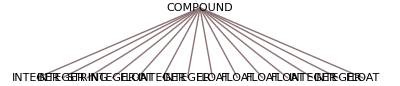

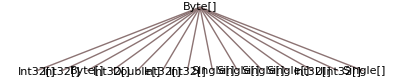

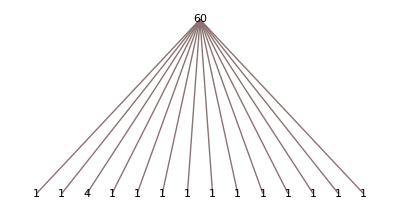

```mathematica
CompoundDataTypeInformationTree[filename,namesCompoundTypeDataSet[[1]]]
```

### Read Data

```mathematica
namesCompoundTypeDataSet[[2]]
```

./MODIS_SWATH_Type_L1B/Data Fields/Band_250M

```mathematica
ReadAttributes[filename,namesCompoundTypeDataSet[[2]]]
```

{NumberOfAttributes→7,AttributeName→{CLASS,FIELD_0_NAME,HDF4_OBJECT_NAME,HDF4_OBJECT_TYPE,HDF4_REF_NUM,TITLE,VERSION},AttributeClassType→{STRING,STRING,STRING,STRING,INTEGER,STRING,STRING},AttributeSystemType→{System.Byte[],System.Byte[],System.Byte[],System.Byte[],System.UInt16[],System.Byte[],System.Byte[]},AttributeSystemTypeCountInOneDatum→{5,9,9,5,1,9,3},AttributeSpaceDimensions→{{},{},{},{},{},{},{}},AttributeValues→{TABLE,Band_250M,Band_250M,Vdata,6093,Band_250M,1.0}}

```mathematica
CompoundDataTypeInformation[filename,namesCompoundTypeDataSet[[2]]]
```

{NumberOfMembers→1,MemberName→{Band_250M},MemberClassType→{FLOAT},MemberSystemType→{System.Single[]},MemberSystemTypeCountInOneDatum→{1}}

```mathematica
myFunction[member1Single:_List]:=Map[System`BitConverter`ToSingle[#,0]&][member1Single]
```

```mathematica
ReadHyperSlab[filename,namesCompoundTypeDataSet[[2]],{},{},"ByteConversionFunction"->(myFunction[{##}]&)]
```

{{1.},{2.}}